ⅇ^(4 ⅈ (12+x)-1/16 (12+x)^2)

Piecewise[{{ⅇ^(4 ⅈ (12+x)-1/16 (12+x)^2), -13≤x≤-11}, {0, True}}]

√2 ⅇ^(-4 (16-(8+3 ⅈ) p+p^2)) (Erf[(1/4+8 ⅈ)-2 ⅈ p]-ⅈ Erfi[(8+ⅈ/4)-2 p])

Piecewise[{{ⅇ^(4 ⅈ (12+x)-1/16 (12+x)^2), x≤-13||x≥-11}, {0, True}}]

-√2 ⅇ^(-4 (16-(8+3 ⅈ) p+p^2)) (-2+Erf[(1/4+8 ⅈ)-2 ⅈ p]-ⅈ Erfi[(8+ⅈ/4)-2 p])

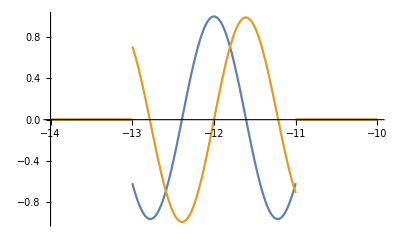

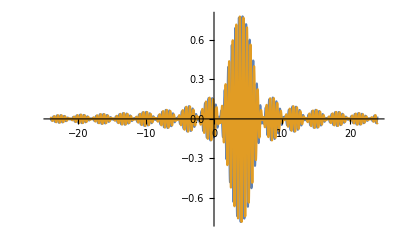

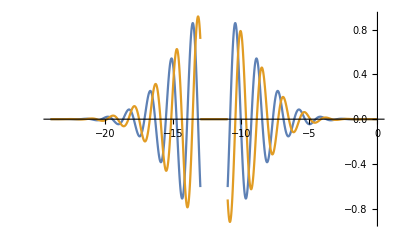

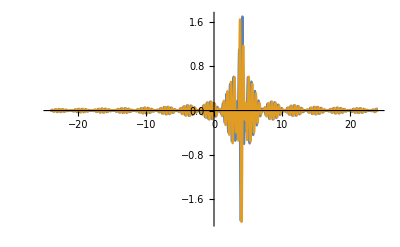

```mathematica
ћ=1;
a=4;
x0=-12;
p0=4;
xRange=2;
ψ=Exp[-((x-x0)/a)^2+ⅈ p0(x-x0)/ћ]
ψ1=Piecewise[{{ψ,x0-xRange/2≤x≤x0+xRange/2}}]
ϕ1=InverseFourierTransform[ψ1,x,p]
ψ2=Piecewise[{{ψ,x≤x0-xRange/2},{ψ,x≥x0+xRange/2}}]
ϕ2=InverseFourierTransform[ψ2,x,p]
Plot[{Re[ψ1],Im[ψ1]},{x,x0-xRange/2-1,x0+xRange/2+1},PlotRange->All,PlotPoints->150]
Plot[{Re[ϕ1],Im[ϕ1]},{p,-p0-20,p0+20},PlotRange->All,PlotPoints->150]
Plot[{Re[ψ2],Im[ψ2]},{x,-3a+x0,3a +x0},PlotRange->All,PlotPoints->150]
Plot[{Re[ϕ2],Im[ϕ2]},{p,-p0-20,p0+20},PlotRange->All,PlotPoints->150]
```